## Using PRIMAT. Custom plots for companion paper

### Loading PRIMAT

Setting the notebook directory (in batch mode this is not evaluated because it seems to be the default one)

```mathematica
SetDirectory[NotebookDirectory[]];
```

Then we go the parent directory, or base directory of PRIMAT.

```mathematica
SetDirectory[ParentDirectory[Directory[]]]
```

/Users/pitrou/Dropbox/iap/notebooks/BBN

We load PRIMAT. It takes some time because it starts reading the file with nuclear reactions and deduces which are the nuclides needed, 
and it starts to build formally the network of equations

```mathematica
Timing[<<PRIMAT-Main.m]
```

{16.8608,Null}

### High temperature results for neutron abundance

Tight coupling expansion. This is based on the method developped in [Bernstein et al. 1989], Eq. 2.8. 
Essentially it is a simple Tight-Coupling expansion, where the lowest order is the equilibrium solution. 
This is reinjected in the equation to get the first order correction, and then in turn reinjected to get the second order etc..

This method is detailed in the companion paper.

The n - th order is obtained by reinjecting the (n - 1) - th order

```mathematica
TCn[0][tv_]:=With[{T=Tofa@aoft@tv},LpTOn[T]/(LnTOp[T]+LpTOn[T])];
TCn[n_Integer][tv_]:=With[{T=Tofa@aoft@tv},-1/(LnTOp[T]+LpTOn[T])*TCn[n-1]'[tv]]/;n>0;
```

The total solution is the sum of all orders up to a desired order. We also define the difference with the numerical value to check how the precision is improved by going to higher and higher orders.

```mathematica
SolTCn[n_Integer][tv_]:=Sum[TCn[i][tv],{i,0,n}];
RelativeDifferenceYn[n_][tv_]:=(SolTCn[n][tv]-YI["n"][tv])/YI["n"][tv];
```

We plot the first few tight - coupling solutions

```mathematica
MyTickst={{Automatic,Automatic},{Automatic,{{tofa@a[10^11],"10^11K"},{tofa@a[10^10.5],"10^10.5K"},{tofa@a[10^10],"10^10K"},{tofa@a[10^9.5],"10^9.5K"},{tofa@a[10^9],"10^9K"},{tofa@a[10^8.5],"10^8.5K"},{tofa@a[10^8],"10^8K"}}}};
```

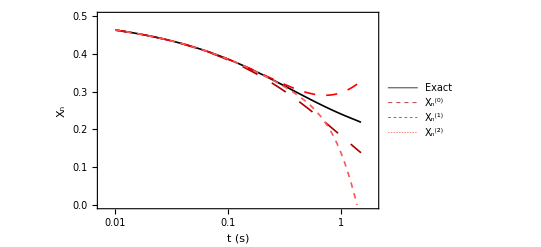

```mathematica
NP1=LogLinearPlot[{YHT["n"][tv],SolTCn[0][tv],SolTCn[1][tv],SolTCn[2][tv]},{tv,t0,1.5},Frame->True,FrameStyle->Thickness[0.004],PlotRange->{0,0.5},FrameLabel->{"t (s)","X_n"},LabelStyle->{FontSize->12},PlotStyle->{{Black,Thickness[0.003]},{Dashing[0.03],Thickness[0.003],Darker@Red},{Dashing[0.02],Thickness[0.003],Red},{Dashing[0.01],Thickness[0.003],Lighter@Red}},GridLines->{{{tofa@a@TFreeze,{Gray,Thickness[0.005]}}},{}},FrameTicks->MyTickst(*,ImageSize->72*6*),ImagePadding->{{40,10},{40,25}},PlotLegends->Placed[LineLegend[{"Exact","X_n^(0)","X_n^(1)","X_n^(2)"},LegendLayout->(Grid[#,Frame->None]&)],Right]]

Export["Plots/PlotTC.pdf",Style[NP1,Magnification->1],"PDF"];
```

We plot the difference between the numerical solution and the tight - coupling solutions

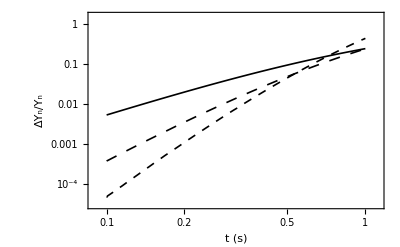

```mathematica
LogLogPlot[{Abs@RelativeDifferenceYn[0][tv],Abs@RelativeDifferenceYn[1][tv],Abs@RelativeDifferenceYn[2][tv]},{tv,0.1,tmiddle},Frame->True,FrameLabel->{"t (s)","ΔY_n/Y_n"},PlotRange->{-0.1,0.1},PlotStyle->{{Black,Thickness[0.003]},{Dashing[0.02],Thickness[0.003],Black},{Dashing[0.015],Thickness[0.003],Black},{Dashing[0.01],Thickness[0.003],Black}}]
```

### Freeze out

```mathematica
HN[t_]:=(D[a[Toft[tv]],tv]/a[Toft[tv]])/.tv->t;
```

```mathematica
LnTOpBORN[T_]:=λnTOpBORN[T]*(τneutron λBORN)^-1
LpTOnBORN[T_]:=λpTOnBORN[T]*(τneutron λBORN)^-1
```

```mathematica
TFreeze=0.8 MeV/kB;
kB TFreeze /MeV
```

0.8

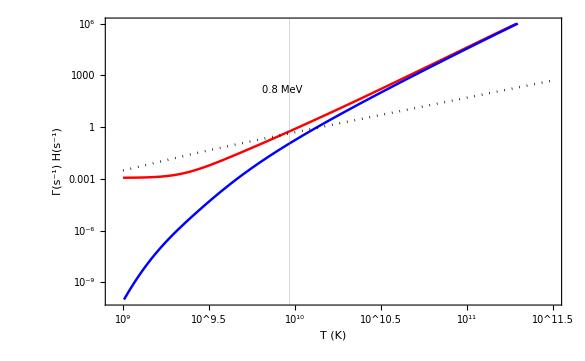

```mathematica
Show[ListLogLogPlot[{Table[{T,LnTOp[T]},{T,ListTRange[10^9,10^11.5]}],Table[{T,LpTOn[T]},{T,ListTRange[10^9,10^11.5]}],(*Table[{T,λnTOpBORN[T]*(τneutron λBORN)^-1},{T,ListTRange[10^9,10^11.5]}],Table[{T,λpTOnBORN[T]*(τneutron λBORN)^-1},{T,ListTRange[10^9,10^11.5]}],*)Table[{T,HN[tofa[a[T]]]},{T,ListTRange[10^9,10^11.5]}](*,Table[{T,Exp[-Q/kB/T]LnTOp[T]},{T,ListTRange[10^9,10^11.5]}]*)},Joined->True,Frame->True,FrameStyle->Thickness[0.003],LabelStyle->{FontSize->12},FrameTicks->MyFrameTicksLog,FrameLabel->{"T (K)","Γ(s^-1)      H(s^-1)"},GridLines->{{{TFreeze,{Gray,Thickness[0.005]}}},{}},PlotStyle->{{Red,Thickness[0.003]},{Blue,Thickness[0.003]},(*{Black,Thickness[0.003],Dashed},{Black,Thickness[0.003],Dashed},*){Black,Thickness[0.003],Dotted},{Black,Thickness[0.003],Dotted}},PlotRange->{10^-10,10^6}],
Graphics[{Rotate[Text[Style["0.8 MeV",FontSize->10,Black],{Log@TFreeze-.1,5}],90 Degree]}]]

Export["Plots/PlotLambdaH.pdf",Style[%,Magnification->1],"PDF"];
```

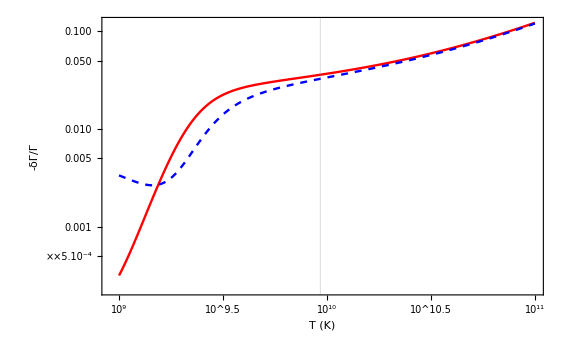

```mathematica
ListLogLogPlot[{Table[{T,Abs[LnTOp[T]/LnTOpBORN[T]-1]},{T,ListTRange[10^9,10^11]}],Table[{T,Abs[LpTOn[T]/LpTOnBORN[T]-1]},{T,ListTRange[10^9,10^11]}]},Joined->True,Frame->True,FrameStyle->Thickness[0.004],FrameTicks->MyFrameTicksLog,FrameLabel->{"T (K)","-δΓ/Γ"},LabelStyle->{FontSize->12},GridLines->{{{TFreeze,{Gray,Thickness[0.005]}}},{}},PlotStyle->{{Red,Thickness[0.003]},{Blue,Thickness[0.003],Dashed}}]

Export["Plots/PlotDeltaLambda.pdf",Style[%,Magnification->1],"PDF"];
```

```mathematica
Tfreeze1=FindRoot[{LnTOp[T]==HN[tofa[a[T]]]},{T,10^10}][[1,2]]
Tfreeze2=FindRoot[{LnTOp[T]+LpTOn[T]==(Exp[Q/(kB T)]/(1+Exp[Q/(kB T)]))Q/(kB T)HN[tofa[a[T]]]},{T,10^10}][[1,2]]
```

8.29208×10^9

8.93146×10^9

### Checks for the chemical potential of electrons/positrons

Throughout we assumed that μ_e/T is negligible. But it is not really True. When m_e/T>26, μ_e/T starts to be sizable (>1). However this is harmless.

Let us determine the chemical potential

```mathematica
nγ[T_]:=2 Zeta[3]/Pi^2  (kB T)^3/(hbar clight)^3;(*cm^-3*)
(*ργ[T_]:=2 Pi^2/30  T^4(kB T)^4/(hbar^3 clight^5)(*g cm^-3*)*)
```

```mathematica
IFD[m_,n_][x_,y_?NumericQ]:=NIntegrate[u^m(u^2-x^2)^(n/2)/(Exp[u-y]+1),{u,x,Infinity}]
nelectrons[T_,y_]:=2/(2π^2)(kB T)^3/(hbar clight)^3Simplify[IFD[1,1][me/(kB T),y]]/;T≥0;
(*ρelectrons[T_,y_]:=2/(2π^2)(kB T)^4/(hbar^3 clight^5)Simplify[IFD[2,1][me/(kB T),y]]/;T≥0;*)
```

```mathematica
Clear[μofT]
μofT[T_]:=μofT[T]=Module[{Y},
Y=y/.FindRoot[FullSimplify[nelectrons[T,y]-nelectrons[T,-y]]==YI["p"][tofa@a[T]]nbaryons0/(a[T])^3,{y,me/(kB T)}][[1]];Y]

Clear[μofTCrude]
μofTCrude[T_]:=μofTCrude[T]=Module[{Y},
Y=y/.FindRoot[FullSimplify[nelectrons[T,y]-nelectrons[T,-y]]== 1/(1+Exp[-Q/(kB T)])ηfactor (nγ[T]+nelectrons[T,y]+nelectrons[T,-y]),{y,me/(kB T)}][[1]];Y]
```

```mathematica
ListTempChemicalPotential=Table[10^lTv,{lTv,8,11,0.1/4}];
```

```mathematica
TableTμ=Table[{Tv,μofT[Tv]},{Tv,ListTempChemicalPotential}];
TableTμAnalytic=Table[{Tv,With[{x=me/(kB Tv)},(*x-Log[Sqrt[Pi/2]x^(3/2)/(2 ηfactor (1-0.12) Zeta[3])*)ArcSinh[(ηfactor (1-0.12) ⅇ^x 2Zeta[3] π^(3/2))/(√2 x^(3/2)Pi^2)]]},{Tv,ListTempChemicalPotential}];
TableTμCrude=Table[{Tv,μofTCrude[Tv]},{Tv,ListTempChemicalPotential}];
TableTnelec=Table[{Tv,nelectrons[Tv,μofT[Tv]]/(3Zeta[3]/(2 π^2)(kB Tv)^3/(hbar clight)^3)},{Tv,ListTempChemicalPotential}];
TableTnelecNoμ=Table[{Tv,nelectrons[Tv,0]/(3Zeta[3]/(2 π^2)(kB Tv)^3/(hbar clight)^3)},{Tv,ListTempChemicalPotential}];
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

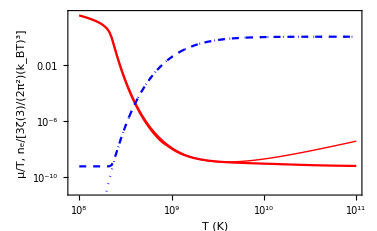

```mathematica
PlotChemicalPotential=ListLogLogPlot[{TableTμ,TableTμAnalytic,TableTnelec,TableTnelecNoμ},Joined->True,Frame->True,FrameLabel->{"T (K)","μ/T,      n_e/[3ζ(3)/(2π^2)(k_BT)^3]"},LabelStyle->{FontSize->12},FrameStyle->Thickness[0.004],PlotStyle->{{Red},{Red,Thin},{Blue,Dashed},{Blue,Dotted}},PlotRange->{10^-11,40},FrameTicks->{{Automatic,Automatic},{{{Log[10^8],"10^8"},{Log[10^8.5],"10^8.5"},{Log[10^9],"10^9"},{Log[10^9.5],"10^9.5"},{Log[10^10],"10^10"},{Log[10^10.5],"10^10.5"},{Log[10^11],"10^11"}},Automatic}},ImagePadding->{{60,10},{40,25}}]

Export["Plots/ChemicalPotential.pdf",Style[PlotChemicalPotential,Magnification->1],"PDF"];
```